```mathematica
FirstDataSet = ReadList["C:\\Users\\Администратор\\Desktop\\krs\\FirstDataSet.txt",{Number,Number}];
SecondDataSet = ReadList["C:\\Users\\Администратор\\Desktop\\krs\\SecondDataSet.txt",{Number,Number}];
```

```mathematica
F[x_, ww_, vv_, aa_] := (
Sum[aa[[icc]] * LogisticSigmoid[ww[[icc]]*x + vv[[icc]]], {icc,1,Length[aa]}]
);
Q[x_, y_, ww_, vv_, aa_] := (
(Sum[aa[[icc]] * LogisticSigmoid[ww[[icc]]*x + vv[[icc]]], {icc,1,Length[aa]}] - y)^2
);
```

```mathematica
n = 200;
w = Table[RandomReal[], {i, 1, n}];
v = Table[RandomReal[], {i, 1, n}];
a = Table[RandomReal[], {i, 1, n}];
```

```mathematica
dataSet = FirstDataSet;
```

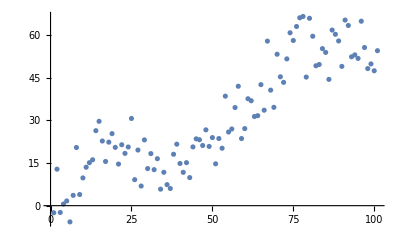

```mathematica
Show[ListPlot[dataSet],Plot[F[x,w,v,a],{x, 0, 100}, PlotStyle->{Red}] ]
```

```mathematica
CalcMPRC2[xIn_,wjhIn_,whmIn_] := (
uih = LogisticSigmoid[xIn.wjhIn];
duih = uih*(ConstantArray[1,Length[uih]] - uih);

uihTemp = Append[uih, 1];

am = uihTemp.whmIn
);
```

```mathematica
количество входов;
j = 2;
количество нейронов в скрытом слое;
h = 30;
DataSet = SecondDataSet;
TrainingSet = RandomSample[DataSet, 30];
wjh = Table[Table[RandomReal[],{hh,1,h}],{jj ,1,j}];
whm = Table[RandomReal[],{hh ,1,h + 1}];

X = Transpose[{Transpose[TrainingSet][[1]], ConstantArray[1, Length[TrainingSet]]}];
Y = Transpose[TrainingSet][[2]];
n1 = 0.01;
n2=0.01;
nevyazki = {};
nny = {};
```

```mathematica
n1 = 0.001;
n2=n1;
```

```mathematica
counter=0;
nevyazka = 2001;
While[nevyazka >300
,
nevyazka = 0;
For[cCounter = 1, cCounter <Length[X], cCounter++,
xi = X[[cCounter]];
yi = Y[[cCounter]];

(*прямой ход;*)

uih = LogisticSigmoid[xi.wjh];
duih = uih*(ConstantArray[1,Length[uih]] - uih);

uihTemp = Append[uih, 1];

am = uihTemp.whm;

e = am - yi;
eQ = e^2;
nevyazka += eQ;
(*обратный ход;*)

ehi=e*whm;


(*градиентный шаг;*)

whm -= n2*e*uihTemp;
wjh-= n1*Table[Table[n2*ehi[[hh]]*duih[[hh]]*xi[[jj]],{hh,1,h}],{jj ,1,j}]


];
counter++;
If[Mod[counter, 1000] == 0,
PrintTemporary[nevyazka];
];

AppendTo[nevyazki, nevyazka];

];
```

$Aborted

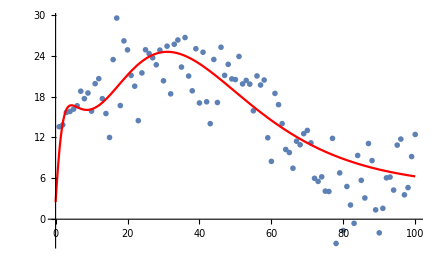

```mathematica
Show[ListPlot[DataSet], Plot[CalcMPRC2[{x,1}, wjh, whm],{x,0,100}, PlotStyle->{Red}]]
```

```mathematica
ListPlot[nevyazki, Joined->True]
```

-Graphics-